```mathematica
wd=NotebookDirectory[];
SetDirectory[wd]
```

/home/jacob/projects/quonium/mathematica

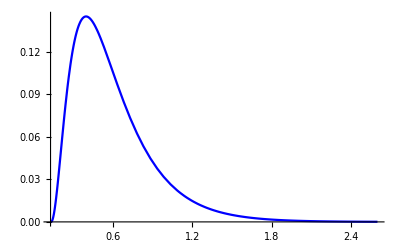

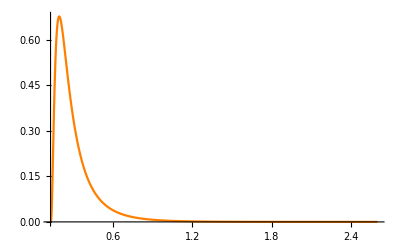

```mathematica
(*State mass*)
M=9.460;
(**)
Enl=0.130;
T=0.3;
CF=4/3;
NC=3;
αs=0.3;
aB=2/(αs*CF*M);
prel[q_]:=Sqrt[M(q-Enl)];


η[q_]:=αs*M/(4*NC*prel[q])

OvLp1S[q_]:=(((2^9)(Pi^2)(η[q])(aB^7)(prel[q]^2)(1+η[q]^2)(2+η[q]*aB*prel[q])^2)/((1+(aB^2)(prel[q]^2))^6(Exp[2Pi*η[q]]-1)))*Exp[4η[q]*ArcTan[aB*prel[q]]];
OvLp2S[q_]:=(((2^18)(Pi^2)(η[q])(aB^7)(prel[q]^2)(1+η[q]^2))/((1+4(aB^2)(prel[q]^2))^6(Exp[2Pi*η[q]]-1)))*Exp[4η[q]*ArcTan[2aB*prel[q]]];

Ig1S[q_]:=Piecewise[{{(q^3)*prel[q](1/(Exp[q/T]-1))OvLp1S[q],q>Enl},{0,q<=Enl}}];
Ig2S[q_]:=Piecewise[{{(q^3)*prel[q](1/(Exp[q/T]-1))OvLp2S[q],q>Enl},{0,q<=Enl}}];

IGP1S=Plot[Ig1S[q],{q,Enl,20Enl},PlotRange->All,PlotStyle->Blue]
IGP2S=Plot[Ig2S[q],{q,Enl,20Enl},PlotRange->All,PlotStyle->Orange]
```

```mathematica
Ig1S[50Enl]
Ig2S[50Enl]
```

6.94846×10^-11

2.52505×10^-12

```mathematica
MaxE=50*Enl;
```

```mathematica
RejSample[dist1V_,dmax_]:=Module[{ReSamp,qtry},
ReSamp=True;
While[ReSamp,
qtry=RandomReal[{Enl,20Enl}];
If[RandomReal[]<dist1V[qtry]/dmax,ReSamp=False];
];
qtry
];
maxqVal1S=Maximize[{Ig1S[q],Enl<q<20Enl},q][[1]]
maxqVal2S=Maximize[{Ig2S[q],Enl<q<20Enl},q][[1]]
```

0.145043

0.677364

```mathematica
Samp1S=Table[RejSample[Ig1S,maxqVal1S],{i,1,10000}];
Samp2S=Table[RejSample[Ig2S,maxqVal2S],{i,1,10000}];
```

```mathematica
stp=0.01;
Int1Tdat1S=Table[Ig1S[qi],{qi,Enl,MaxE,stp}];
Int1Dat1S=Join[{{Enl,MaxE}},Int1Tdat1S];
Export["../interpolations/RGAqInt1S.tsv",Int1Dat1S]

Int1Tdat2S=Table[Ig2S[qi],{qi,Enl,MaxE,stp}];
Int1Dat2S=Join[{{Enl,MaxE}},Int1Tdat2S];
Export["../interpolations/RGAqInt2S.tsv",Int1Dat2S]
```

../interpolations/RGAqInt1S.tsv

../interpolations/RGAqInt2S.tsv

```mathematica
IgNorm1S=NIntegrate[Ig1S[q],{q,Enl,50Enl}]
IgNorm2S=NIntegrate[Ig2S[q],{q,Enl,50Enl}]
```

0.0826777

0.128217

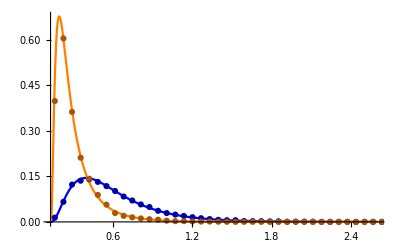

```mathematica
bspec=Table[Enl*i,{i,1,50,0.5}];
SampRate=Length[bspec];
HLS1S=HistogramList[Samp1S,{bspec}];
HLS2S=HistogramList[Samp2S,{bspec}];
SampHist1S=ListPlot[Table[{(HLS1S[[1,i]]+HLS1S[[1,i-1]])/2,IgNorm1S*HLS1S[[2,i-1]]/(Total[HLS1S[[2]]]*(bspec[[2]]-bspec[[1]]))},{i,2,Length[HLS1S[[1]]]}],PlotStyle->Darker[Blue]];
SampHist2S=ListPlot[Table[{(HLS2S[[1,i]]+HLS2S[[1,i-1]])/2,IgNorm2S*HLS2S[[2,i-1]]/(Total[HLS2S[[2]]]*(bspec[[2]]-bspec[[1]]))},{i,2,Length[HLS2S[[1]]]}],PlotStyle->Darker[Orange]];
Show[IGP1S,IGP2S,SampHist1S,SampHist2S,PlotRange->{{Enl,20Enl},All}]
```